## Солитоны

#### 1

```mathematica
sol=DSolve[D[u[x,t],{x,3}]+D[u[x,t],t]+6u[x,t]D[u[x,t],x]==0,u[x,t],{x,t}][[1,1,2]]
```

DSolve::nlpde: Solution requested to nonlinear partial differential equation. Trying to build a special solution.

-(-8 C[1]^3+C[2]+12 C[1]^3 Tanh[x C[1]+t C[2]+C[3]]^2)/(6 C[1])

```mathematica
c1=0.1;c2=0.1;c3=0.1;
```

```mathematica
Plot3D[sol/.{C[1]->1,C[2]->1,C[3]->1},{x,-5,5},{t,-5,5},PlotRange->All]
```

-Graphics3D-

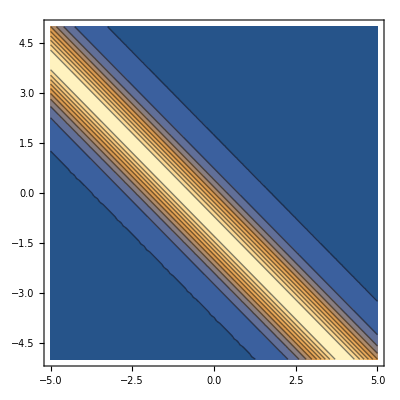

```mathematica
ContourPlot[sol/.{C[1]->1,C[2]->1,C[3]->1},{x,-5,5},{t,-5,5},PlotRange->All]
```

```mathematica
res1=sol/.{C[1]->1,C[2]->1,C[3]->1};
```

```mathematica
D[res1,{x,3}]+D[res1,t]+6res1 D[res1,x]
```

-4 Sech[1+t+x]^2 Tanh[1+t+x]-4 Sech[1+t+x]^2 Tanh[1+t+x] (7-12 Tanh[1+t+x]^2)-2 (-16 Sech[1+t+x]^4 Tanh[1+t+x]+8 Sech[1+t+x]^2 Tanh[1+t+x]^3)

```mathematica
sol/.{C[1]->1,C[2]->1,C[3]->1}
```

1/6 (7-12 Tanh[1+t+x]^2)

#### 2

```mathematica
A=((a1-a2)/(a1+a2))^2;
ο1[x,t]=-t a1^3+x a1+θ1;
ο2[x,t]=-t a2^3+x a2+θ2;
f1[x,t]=Exp[ο1[x,t]];
f2[x,t]=Exp[ο2[x,t]];
F[x,t]=1+f1[x,t]+f2[x,t]+A f2[x,t]f1[x,t]
```

1+ⅇ^(-a1^3 t+a1 x+θ1)+ⅇ^(-a2^3 t+a2 x+θ2)+((a1-a2)^2 ⅇ^(-a1^3 t-a2^3 t+a1 x+a2 x+θ1+θ2))/(a1+a2)^2

```mathematica
u[x,t]=D[Log[F[x,t]],{x,2}];
```

```mathematica
res2=u[x,t]/.{a1->1,a2->1,θ1->0,θ2->0}
```

-(4 ⅇ^(-2 t+2 x))/((1+2 ⅇ^(-t+x))^2)+(2 ⅇ^(-t+x))/(1+2 ⅇ^(-t+x))

```mathematica
res2//Simplify
```

(2 ⅇ^(t+x))/((ⅇ^t+2 ⅇ^x)^2)

```mathematica
qq=D[res2,{x,3}]+D[res2,t]+6res2 D[res2,x]//FullSimplify
```

(24 ⅇ^(2 (t+x)) (-ⅇ^t+2 ⅇ^x))/((ⅇ^t+2 ⅇ^x)^5)

```mathematica
Plot3D[res2,{x,-5,5},{t,-5,5}]
```

-Graphics3D-

#### 3

```mathematica
u[x,t]//FullSimplify
```

(2 (a1+a2)^2 ⅇ^((a1^3+a2^3) t+(a1+a2) x+θ1+θ2) (a1^4-2 a1^2 a2^2+a2^4+a2^2 (a1^2+a2^2) Cosh[a1^3 t-a1 x-θ1]+a1^2 (a1^2+a2^2) Cosh[a2^3 t-a2 x-θ2]+2 a1 a2^3 Sinh[a1^3 t-a1 x-θ1]+2 a1^3 a2 Sinh[a2^3 t-a2 x-θ2]))/((a1+a2)^2 ⅇ^(a2^3 t) (ⅇ^(a1^3 t)+ⅇ^(a1 x+θ1))+ⅇ^(a2 x+θ2) ((a1+a2)^2 ⅇ^(a1^3 t)+(a1-a2)^2 ⅇ^(a1 x+θ1)))^2

```mathematica
Manipulate[Plot3D[u[x,t]/.{a1->a11,a2->a22,θ1->θ11,θ2->θ22},{x,-20,20},{t,-20,20},PlotRange->All,MeshFunctions->{30#1 & , 30#2 & },Mesh->150],{a11,0.1,3},{a22,0.1,3},{θ11,-4,4},{θ22,-4,4}]
```